-Graphics-

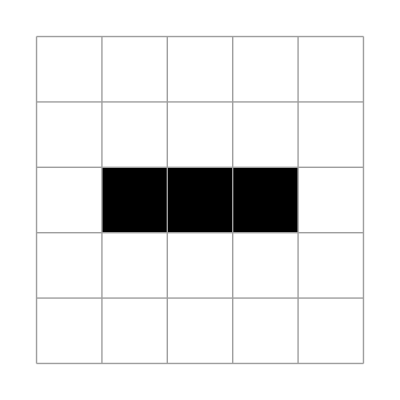

```mathematica
lr;
stateX=bool[({{x[1,1], x[1,2], x[1,3], x[1,4], x[1,5]}, {x[2,1], x[2,2], x[2,3], x[2,4], x[2,5]}, {x[3,1], x[3,2], x[3,3], x[3,4], x[3,5]}, {x[4,1], x[4,2], x[4,3], x[4,4], x[4,5]}, {x[5,1], x[5,2], x[5,3], x[5,4], x[5,5]}})=loob[({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})]];
Clear[x];
stateXPrime=bool[({{xp[1,1], xp[1,2], xp[1,3], xp[1,4], xp[1,5]}, {xp[2,1], xp[2,2], xp[2,3], xp[2,4], xp[2,5]}, {xp[3,1], xp[3,2], xp[3,3], xp[3,4], xp[3,5]}, {xp[4,1], xp[4,2], xp[4,3], xp[4,4], xp[4,5]}, {xp[5,1], xp[5,2], xp[5,3], xp[5,4], xp[5,5]}})=loob[({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})]];
plt[stateX]
```

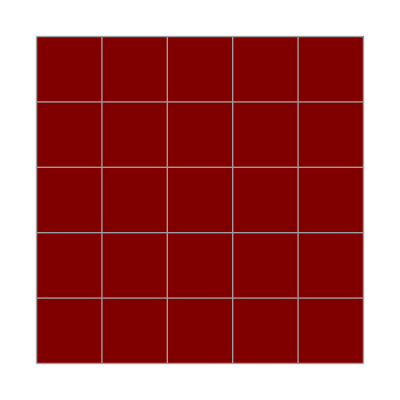

```mathematica
Clear[i,j];
(*x[0,_]=False;
x[_,0]=False;

x[_,6]=False;
x[6,_]=False;*)

Array[

formula

,{5,5}]//bool//plt
```

```mathematica
formula
```

```mathematica
SearchStillLife[w_,h_]:=Block[{r=RandomChoice[{True,False},{w,h}]},MapThread[Xor,{r,ArrayReshape[SatisfiabilityInstances[Array[StillLifeCondition[##]/.b[i_,j_]/;i<1||i>w||j<1||j>h:>False/.b[i_,j_]:>Xor[b[i,j],r[[i,j]]]&,{w,h}+2,0,And],Catenate[Array[b,{w,h}]]][[1]],{w,h}]},2]]
```

```mathematica
SatisfiabilityInstances[Array[StillLifeCondition[##]/.b[i_,j_]/;i<1||i>w||j<1||j>h:>False/.b[i_,j_]:>Xor[b[i,j],r[[i,j]]]&,{w,h}+2,0,And],Catenate[Array[b,{w,h}]]]
```

```mathematica
SatisfiabilityInstances[formula]
```

SatisfiabilityInstances::bfun: and[{Nothing,«17»,!x[SlotSequence[«1»]]&&count[{8},{SlotSequence[«1»]}]⇒!xp[##1]}]& is not a Boolean-valued pure function.

```mathematica
form=and@Flatten@Array[

formula

,{5,5}];
```

```mathematica
varlist=Catenate@Array[x,{5,5}];
```

```mathematica
lr
```

```mathematica
bool[Array[x,{5,5}]/.Thread[varlist->SatisfiabilityInstances[form,varlist][[1]]]
]//Grid
```

1 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0

```mathematica
life44
```

```mathematica
X1=({{1, 1, 0, 1, 1}, {0, 0, 0, 0, 0}, {1, 1, 1, 1, 1}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}})//FullForm
```

Grid[List[List[1,1,0,1,1],List[0,0,0,0,0],List[1,1,1,1,1],List[0,0,1,0,0],List[0,0,1,0,0]],Rule[ItemSize,List[Automatic,Automatic]]]

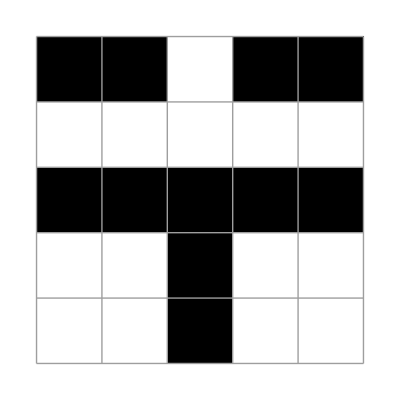
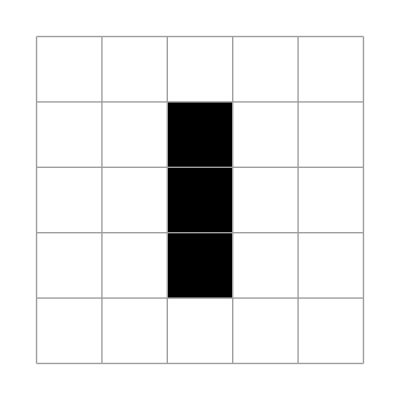
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
X1=({{1, 1, 0, 1, 1}, {0, 0, 0, 0, 0}, {1, 1, 1, 1, 1}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}})[[1]];
MessageDialog[X1];
plt/@NestList[updateLife2[{5,5}][ #]&,
X1,3]
```